-0.373011+1.53853×10^-6 x

-0.126987+1.14141×10^-6 x+4.604×10^-14 x^2

-0.0615581+9.06049×10^-7 x+1.15993×10^-13 x^2-4.91464×10^-21 x^3

-0.0222793+6.73151×10^-7 x+2.46674×10^-13 x^2-2.70187×10^-20 x^3+1.14236×10^-27 x^4

0.000327011+2.62645×10^-7 x+1.06888×10^-12 x^2-6.3221×10^-19 x^3+2.20885×10^-25 x^4-4.36496×10^-32 x^5+4.82736×10^-39 x^6-2.78724×10^-46 x^7+6.54442×10^-54 x^8

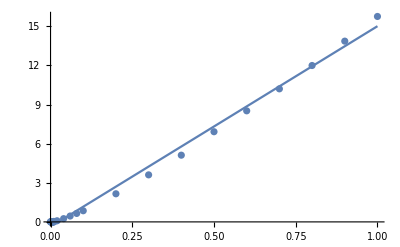

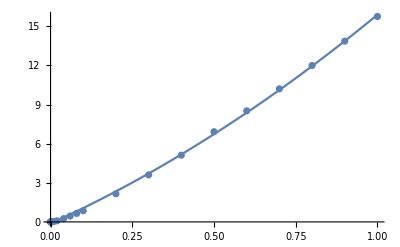

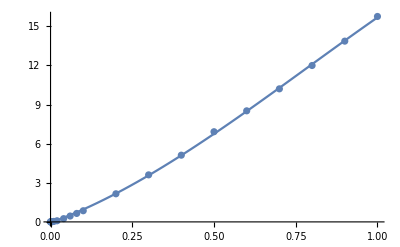

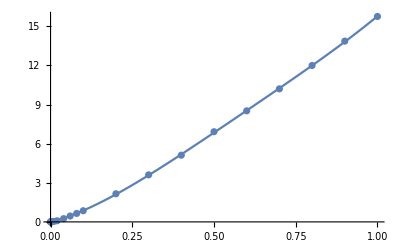

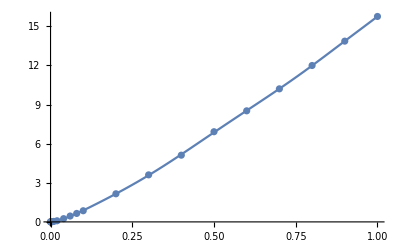

```mathematica
abb1=Fit[{{100,0.0000159740447998046},{1000,0.0001719},{5000,0.001017094},{10000,0.002295017},{50000,0.015423059},{100000,0.036169},{200000,0.08591},{400000,0.249607086},{600000,0.449668169},{800000,0.649112225},{1000000,0.855236},{2000000,2.156502962},{3000000,3.60809207},{4000000,5.117367029},{5000000,6.917185783},{6000000,8.520278931},{7000000,10.20669103},{8000000,11.99638486},{9000000,13.86554408},{10000000,15.75872302}},{1,x},x]

abb2=Fit[{{100,0.0000159740447998046},{1000,0.0001719},{5000,0.001017094},{10000,0.002295017},{50000,0.015423059},{100000,0.036169},{200000,0.08591},{400000,0.249607086},{600000,0.449668169},{800000,0.649112225},{1000000,0.855236},{2000000,2.156502962},{3000000,3.60809207},{4000000,5.117367029},{5000000,6.917185783},{6000000,8.520278931},{7000000,10.20669103},{8000000,11.99638486},{9000000,13.86554408},{10000000,15.75872302}},{1,x,x^2},x]

abb3=Fit[{{100,0.0000159740447998046},{1000,0.0001719},{5000,0.001017094},{10000,0.002295017},{50000,0.015423059},{100000,0.036169},{200000,0.08591},{400000,0.249607086},{600000,0.449668169},{800000,0.649112225},{1000000,0.855236},{2000000,2.156502962},{3000000,3.60809207},{4000000,5.117367029},{5000000,6.917185783},{6000000,8.520278931},{7000000,10.20669103},{8000000,11.99638486},{9000000,13.86554408},{10000000,15.75872302}},{1,x,x^2,x^3},x]

abb4=Fit[{{100,0.0000159740447998046},{1000,0.0001719},{5000,0.001017094},{10000,0.002295017},{50000,0.015423059},{100000,0.036169},{200000,0.08591},{400000,0.249607086},{600000,0.449668169},{800000,0.649112225},{1000000,0.855236},{2000000,2.156502962},{3000000,3.60809207},{4000000,5.117367029},{5000000,6.917185783},{6000000,8.520278931},{7000000,10.20669103},{8000000,11.99638486},{9000000,13.86554408},{10000000,15.75872302}},{1,x,x^2,x^3,x^4},x]

abb8=Fit[{{100,0.0000159740447998046},{1000,0.0001719},{5000,0.001017094},{10000,0.002295017},{50000,0.015423059},{100000,0.036169},{200000,0.08591},{400000,0.249607086},{600000,0.449668169},{800000,0.649112225},{1000000,0.855236},{2000000,2.156502962},{3000000,3.60809207},{4000000,5.117367029},{5000000,6.917185783},{6000000,8.520278931},{7000000,10.20669103},{8000000,11.99638486},{9000000,13.86554408},{10000000,15.75872302}},{1,x,x^2,x^3,x^4,x^5,x^6,x^7,x^8},x]

puntos=ListPlot[{{100,0.0000159740447998046},{1000,0.0001719},{5000,0.001017094},{10000,0.002295017},{50000,0.015423059},{100000,0.036169},{200000,0.08591},{400000,0.249607086},{600000,0.449668169},{800000,0.649112225},{1000000,0.855236},{2000000,2.156502962},{3000000,3.60809207},{4000000,5.117367029},{5000000,6.917185783},{6000000,8.520278931},{7000000,10.20669103},{8000000,11.99638486},{9000000,13.86554408},{10000000,15.75872302}}]

g1=Plot[abb1,{x,0,10000000}]
Show[puntos,g1]

g2=Plot[abb2,{x,0,10000000}]
Show[puntos,g2]

g3=Plot[abb3,{x,0,10000000}]
Show[puntos,g3]

g4=Plot[abb4,{x,0,10000000}]
Show[puntos,g4]

g8=Plot[abb8,{x,0,10000000}]
Show[puntos,g8]
```